```mathematica
temperatures={0.039 ,0.01, 0.00385, 0.002,  0.00025 ,0.00014 ,0.000091, 0.000077 ,0.000054,0.000045 ,0.000036, 0.000024 ,0.000018 ,0.000016 ,0.000014}
```

{0.039,0.01,0.00385,0.002,0.00025,0.00014,0.000091,0.000077,0.000054,0.000045,0.000036,0.000024,0.000018,0.000016,0.000014}

```mathematica
NumberForm[temperatures[[3]],{8,8}]
```

0.00385000

```mathematica
time256=DeleteCases[Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N256/simulationTime/p3.900/simTime&TimeCostForthePreviousTau_N64_p3.9000_T"<>ToString[NumberForm[temperatures[[T]],{8,8}]]<>"_idx0.nc","Data"],{T,Length[temperatures]}],$Failed];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N256/simulationTime/p3.900/simTime&TimeCostForthePreviousTau_N256_p3.9000_T0.03900000_idx0.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N256/simulationTime/p3.900/simTime&TimeCostForthePreviousTau_N256_p3.9000_T0.01000000_idx0.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N256/simulationTime/p3.900/simTime&TimeCostForthePreviousTau_N256_p3.9000_T0.00385000_idx0.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
time=DeleteCases[Table[Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/simulationTime/p3.900/simTime&TimeCostForthePreviousTau_N4096_p3.9000_T"<>ToString[NumberForm[temperatures[[T]],{8,8}]]<>"_idx0.nc","Data"],{T,Length[temperatures]}],$Failed];
```

```mathematica
temperatures[[11]]
```

0.000036

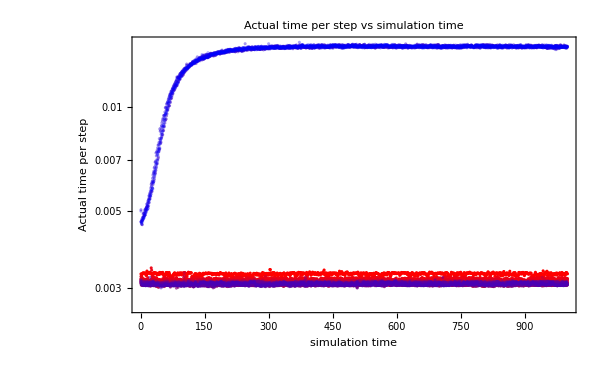

```mathematica
timePlot=ListLogPlot[Table[Table[{time[[T,1,i]],time[[T,2,i]]},{i,1,Length[time[[T,1]]]}],{T,Length[temperatures]}],PlotStyle->redBluePlotConfig[Length[temperatures]],FrameLabel->{"simulation time","Actual time per step"},PlotLabel->"Actual time per step vs simulation time",ImageSize->600]
```

```mathematica
Export["/home/chengling/Research/updates/05092024/timePlot.jpeg",timePlot,ImageResolution->800]
```

/home/chengling/Research/updates/05092024/timePlot.jpeg

```mathematica
timelowT=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/simulationTime/p3.900/simTime&TimeCostForthePreviousTau_N4096_p3.9000_T0.00002400_idx0.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

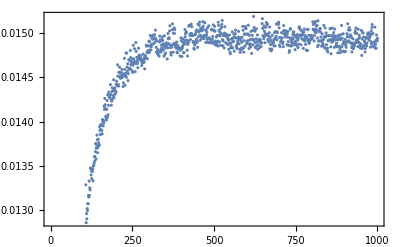

```mathematica
ListPlot[Table[{timelowT[[1,i]],timelowT[[2,i]]},{i,Length[timelowT[[1]]]}]]
```